Case N=6

Parametrizations of the differents matrices are:

```mathematica
e0ϕ[lamb1_,lamb2_,lamb3_,lamb4_,lamb5_]:=1/3*(9*lamb1/2+lamb2+2*lamb3);
e1ϕ[lamb1_,lamb2_,lamb3_,lamb4_,lamb5_]:=1/3*(9*lamb1/2+lamb2-lamb3);
e2ϕ[lamb1_,lamb2_,lamb3_,lamb4_,lamb5_]:=1/3*(9*lamb1/2-2*lamb2-lamb3);
e3ϕ[lamb1_,lamb2_,lamb3_,lamb4_,lamb5_]:=1/3*(-9*lamb1/2+lamb4+2*lamb5);
e4ϕ[lamb1_,lamb2_,lamb3_,lamb4_,lamb5_]:=1/3*(-9*lamb1/2+lamb4-lamb5);
e5ϕ[lamb1_,lamb2_,lamb3_,lamb4_,lamb5_]:=1/3*(-9*lamb1/2-2*lamb4-lamb5);

e0t=1/2*5;
e1t=1/2*3;
e2t=1/2*1;
e3t=1/2*(-1);
e4t=1/2*(-3);
e5t=1/2*(-5);

e0AdS=I/2*5;
e1AdS=I/2*3;
e2AdS=I/2*1;
e3AdS=I/2*(-1);
e4AdS=I/2*(-3);
e5AdS=I/2*(-5);
```

We confirm that the matrices have trace equal to zero

```mathematica
Simplify[e0ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]+e1ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]+e2ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]+e3ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]+e4ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]+e5ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]]
```

0

and the parametrization is proportional to BTZ BH when lamb_i=lamb

```mathematica
Print[Simplify[e0ϕ[lamb,lamb,lamb,lamb,lamb]]];Print[Simplify[e1ϕ[lamb,lamb,lamb,lamb,lamb]]];Print[Simplify[e2ϕ[lamb,lamb,lamb,lamb,lamb]]];Print[Simplify[e3ϕ[lamb,lamb,lamb,lamb,lamb]]];Print[Simplify[e4ϕ[lamb,lamb,lamb,lamb,lamb]]];Print[Simplify[e5ϕ[lamb,lamb,lamb,lamb,lamb]]]
```

(5 lamb)/2

(3 lamb)/2

lamb/2

-lamb/2

-(3 lamb)/2

-(5 lamb)/2

Charges:

```mathematica
Qn[n_,lamb1_,lamb2_,lamb3_,lamb4_,lamb5_]:=1/n*Simplify[e0ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]^n+e1ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]^n+e2ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]^n+e3ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]^n+e4ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]^n+e5ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]^n];
QnAdS[n_]:=1/n*Simplify[e0AdS^n+e1AdS^n+e2AdS^n+e3AdS^n+e4AdS^n+e5AdS^n];
```

BH’s entropy:

```mathematica
S[lamb1_,lamb2_,lamb3_,lamb4_,lamb5_]:=Simplify[e0ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]*e0t+e1ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]*e1t+e2ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]*e2t+e3ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]*e3t+e4ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]*e4t+e5ϕ[lamb1,lamb2,lamb3,lamb4,lamb5]*e5t];
S[lamb1,lamb2,lamb3,lamb4,lamb5]
```

(27 lamb1)/2+lamb2+lamb3+lamb4+lamb5

Action:

```mathematica
Γ[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_, mu3_, mu4_, mu5_, mu6_]:= 5*(Qn[2,lamb1,lamb2,lamb3,lamb4,lamb5] -QnAdS[2])+mu3*(Qn[3,lamb1,lamb2,lamb3,lamb4,lamb5]-QnAdS[3])+mu4*(Qn[4,lamb1,lamb2,lamb3,lamb4,lamb5]-QnAdS[4])+mu5*(Qn[5,lamb1,lamb2,lamb3,lamb4,lamb5]-QnAdS[5])+mu6*(Qn[6,lamb1,lamb2,lamb3,lamb4,lamb5]-QnAdS[6])-S[lamb1,lamb2,lamb3,lamb4,lamb5];
```

```mathematica
Print[QnAdS[2]];
Print[QnAdS[3]];
Print[QnAdS[4]];
Print[QnAdS[5]];
Print[QnAdS[6]];
```

Jacobian matrix of transformation Q -> lamb

```mathematica
dQdlamb[lamb1_,lamb2_,lamb3_,lamb4_,lamb5_,lamb6_]:=1/39366 lamb2 lamb3 (lamb2+lamb3) lamb4 (9 lamb1+lamb2-lamb3-lamb4-2 lamb5) (9 lamb1+lamb2+2 lamb3-lamb4-2 lamb5) (9 lamb1-2 lamb2-lamb3+2 lamb4+lamb5) (9 lamb1-2 lamb2-lamb3-lamb4+lamb5) lamb5 (9 lamb1+lamb2-lamb3-lamb4+lamb5) (9 lamb1+lamb2+2 lamb3-lamb4+lamb5) (lamb4+lamb5) (9 lamb1+lamb2-lamb3+2 lamb4+lamb5) (9 lamb1+lamb2+2 (lamb3+lamb4)+lamb5) (9 lamb1-2 lamb2-lamb3-lamb4-2 lamb5);
```

First derivative of the action Γ

```mathematica
eq1[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_, mu3_, mu4_, mu5_, mu6_]=D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5, mu3, mu4, mu5, mu6],lamb1];
eq2[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_, mu3_, mu4_, mu5_, mu6_]=D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5, mu3, mu4, mu5, mu6],lamb2];
eq3[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_, mu3_, mu4_, mu5_, mu6_]=D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5, mu3, mu4, mu5, mu6],lamb3];
eq4[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_, mu3_, mu4_, mu5_, mu6_]=D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5, mu3, mu4, mu5, mu6],lamb4];
eq5[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_, mu3_, mu4_, mu5_, mu6_]=D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5, mu3, mu4, mu5, mu6],lamb5];
```

We define the intervals of chemical potentials where we will work

```mathematica
mu30=0.1;
mu3f=8;
mu40=0.1;
mu4f=8;
mu50=0.1;
mu5f=8;
mu60=0.1;
mu6f=8;
n=2;
```

```mathematica
emptyTable=Table[0,{mu6,mu60,mu6f,(mu6f-mu60)/n},{mu5,mu50,mu5f,(mu5f-mu50)/n},{mu4,mu40,mu4f,(mu4f-mu40)/n},{mu3,mu30,mu3f,(mu3f-mu30)/n}];
mu3list=Range[mu30,mu3f,(mu3f-mu30)/n];
mu4list=Range[mu40,mu4f,(mu4f-mu40)/n];
mu5list=Range[mu50,mu5f,(mu5f-mu50)/n];
mu6list=Range[mu60,mu6f,(mu6f-mu60)/n];
```

Searching for the global minimum of the action:

```mathematica
Do[{z=NSolve[{
eq1[lamb1, lamb2, lamb3,lamb4,lamb5, mu3list[[v]], mu4list[[u]], mu5list[[y]], mu6list[[x]]]==0,
eq2[lamb1, lamb2, lamb3,lamb4,lamb5, mu3list[[v]], mu4list[[u]], mu5list[[y]], mu6list[[x]]]==0,
eq3[lamb1, lamb2, lamb3,lamb4,lamb5, mu3list[[v]], mu4list[[u]], mu5list[[y]], mu6list[[x]]]==0,
eq4[lamb1, lamb2, lamb3,lamb4,lamb5, mu3list[[v]], mu4list[[u]], mu5list[[y]], mu6list[[x]]]==0,
eq5[lamb1, lamb2, lamb3,lamb4,lamb5, mu3list[[v]], mu4list[[u]], mu5list[[y]], mu6list[[x]]]==0},{lamb1, lamb2, lamb3, lamb4, lamb5},PositiveReals][[1]],emptyTable[[x]][[y]][[u]][[v]]=Qn[2,z[[1]][[2]],z[[2]][[2]],z[[3]][[2]],z[[4]][[2]],z[[5]][[2]]]},{x,1,Length[mu6list]},{y,1,Length[mu5list]},{u,1,Length[mu4list]},{v,1,Length[mu3list]}]
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 1⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
NSolve[{
eq1[lamb1, lamb2, lamb3,lamb4,lamb5, 1,1,1,1]==0,
eq2[lamb1, lamb2, lamb3,lamb4,lamb5,  1,1,1,1]==0,
eq3[lamb1, lamb2, lamb3,lamb4,lamb5, 1,1,1,1]==0,
eq4[lamb1, lamb2, lamb3,lamb4,lamb5,  1,1,1,1]==0,
eq5[lamb1, lamb2, lamb3,lamb4,lamb5, 1,1,1,1]==0,lamb2>0, lamb3>0 ,(lamb2+lamb3)>0 , lamb4>0 , (9 lamb1+lamb2-lamb3-lamb4-2 lamb5)>0 , (9 lamb1+lamb2+2 lamb3-lamb4-2 lamb5)>0 , (-9 lamb1+2 lamb2+lamb3-2 lamb4-lamb5)>0 , (-9 lamb1+2 lamb2+lamb3+lamb4-lamb5) >0 ,lamb5 >0 ,(9 lamb1+lamb2-lamb3-lamb4+lamb5)>0 , (9 lamb1+lamb2+2 lamb3-lamb4+lamb5)>0 , (lamb4+lamb5)>0 , (9 lamb1+lamb2-lamb3+2 lamb4+lamb5)>0 , (9 lamb1+lamb2+2 (lamb3+lamb4)+lamb5)>0 , (-9 lamb1+2 lamb2+lamb3+lamb4+2 lamb5)>0 },{lamb1, lamb2, lamb3, lamb4, lamb5},Reals]
```

{}

```mathematica
Do[NMinimize[{Γ[lamb1, lamb2, lamb3,lamb4,lamb5,  mu3list[[v]], mu4list[[u]], mu5list[[y]], mu6list[[x]]],lamb2>0, lamb3>0 ,(lamb2+lamb3)>0 , lamb4>0 , (9 lamb1+lamb2-lamb3-lamb4-2 lamb5)>0 , (9 lamb1+lamb2+2 lamb3-lamb4-2 lamb5)>0 , (-9 lamb1+2 lamb2+lamb3-2 lamb4-lamb5)>0 , (-9 lamb1+2 lamb2+lamb3+lamb4-lamb5) >0 ,lamb5 >0 ,(9 lamb1+lamb2-lamb3-lamb4+lamb5)>0 , (9 lamb1+lamb2+2 lamb3-lamb4+lamb5)>0 , (lamb4+lamb5)>0 , (9 lamb1+lamb2-lamb3+2 lamb4+lamb5)>0 , (9 lamb1+lamb2+2 (lamb3+lamb4)+lamb5)>0 , (-9 lamb1+2 lamb2+lamb3+lamb4+2 lamb5)>0,50>lamb1,50>lamb2,50>lamb3,50>lamb4,50>lamb5},{lamb1, lamb2, lamb3, lamb4, lamb5},Method->"NelderMead"][[2]],{x,1,Length[mu6list]},{y,1,Length[mu5list]},{u,1,Length[mu4list]},{v,1,Length[mu3list]}]
```

El resto de ecuaciones son

```mathematica
eq6[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_,v1_,v2_,v3_,v4_,v5_, mu3_, mu4_, mu5_, mu6_]=v1*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1],lamb1] + v2*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2],lamb1]  + v3*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb1]  + v4*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb4],lamb1]  + v5*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb5],lamb1] ;
eq7[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_,v1_,v2_,v3_,v4_,v5_, mu3_, mu4_, mu5_, mu6_]=v1*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1],lamb2] + v2*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2],lamb2]  + v3*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb2]  + v4*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb4],lamb2]  + v5*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb5],lamb2] ;
eq8[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_,v1_,v2_,v3_,v4_,v5_, mu3_, mu4_, mu5_, mu6_]=v1*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1],lamb3] + v2*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2],lamb3]  + v3*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb3]  + v4*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb4],lamb3]  + v5*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb5],lamb3] ;
eq9[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_,v1_,v2_,v3_,v4_,v5_, mu3_, mu4_, mu5_, mu6_]=v1*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1],lamb4] + v2*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2],lamb4]  + v3*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb4]  + v4*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb4],lamb4]  + v5*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb5],lamb4] ;
eq10[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_,v1_,v2_,v3_,v4_,v5_, mu3_, mu4_, mu5_, mu6_]=v1*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1],lamb5] + v2*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2],lamb5]  + v3*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb5]  + v4*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb4],lamb5]  + v5*D[D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb5],lamb5] ;
eq11[v1_,v2_,v3_,v4_,v5_]:=v1^2+v2^2+v3^2+v4^2+v5^2;
```

```mathematica
mu4p=1;
mu5p=1;
mu6p=1;
```

Esta solución sol2 se está demorando más de 15 minutos para un solo punto

```mathematica
sol2=NSolve[{
eq1[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4p, mu5p, mu6p]==0,
eq2[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4p, mu5p, mu6p]==0,
eq3[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4p, mu5p, mu6p]==0,
eq4[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4p, mu5p, mu6p]==0,
eq5[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4p, mu5p, mu6p]==0,
eq6[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4p, mu5p, mu6p]==0,
eq7[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4p, mu5p, mu6p]==0,
eq8[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4p, mu5p, mu6p]==0,
eq9[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4p, mu5p, mu6p]==0,
eq10[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4p, mu5p, mu6p]==0,
eq11[v1,v2,v3,v4,v5]==1,
lamb2>0,
lamb3>0,
(lamb2+lamb3)>0,
lamb4>0,
(9 lamb1+lamb2-lamb3-lamb4-2 lamb5)>0,
(9 lamb1+lamb2+2 lamb3-lamb4-2 lamb5)>0,
(9 lamb1-2 lamb2-lamb3+2 lamb4+lamb5)>0,
(9 lamb1-2 lamb2-lamb3-lamb4+lamb5)>0,
lamb5 >0,
(9 lamb1+lamb2-lamb3-lamb4+lamb5)>0,
(9 lamb1+lamb2+2 lamb3-lamb4+lamb5)>0,
(lamb4+lamb5)>0,
(9 lamb1+lamb2-lamb3+2 lamb4+lamb5)>0,
(9 lamb1+lamb2+2 (lamb3+lamb4)+lamb5)>0,
(9 lamb1-2 lamb2-lamb3-lamb4-2 lamb5)>0},{lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5,mu3}]
```

```mathematica
sol2
```

```mathematica
eq12[lamb1_, lamb2_, lamb3_,lamb4_,lamb5_,v1_,v2_,v3_,v4_,v5_, mu3_, mu4_, mu5_, mu6_]=FullSimplify[v1*D[v1*D[v1*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1]+v2*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2]+v3*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb1]+v2*D[v1*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1]+v2*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2]+v3*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb2]+v3*D[v1*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1]+v2*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2]+v3*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb3],lamb1]
+v2*D[v1*D[v1*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1]+v2*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2]+v3*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb1]+v2*D[v1*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1]+v2*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2]+v3*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb2]+v3*D[v1*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1]+v2*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2]+v3*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb3],lamb2]
+v3*D[v1*D[v1*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1]+v2*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2]+v3*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb1]+v2*D[v1*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1]+v2*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2]+v3*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb2]+v3*D[v1*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb1]+v2*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb2]+v3*D[Γ[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4,mu5,mu6],lamb3],lamb3],lamb3]];
```

```mathematica
sol3 = NSolve[{eq1[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4, mu5p, mu6p]==0,
eq2[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4, mu5p, mu6p]==0,
eq3[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4, mu5p, mu6p]==0,
eq4[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4, mu5p, mu6p]==0,
eq5[lamb1, lamb2, lamb3,lamb4,lamb5,mu3,mu4, mu5p, mu6p]==0,
eq6[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4, mu5p, mu6p]==0,
eq7[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4, mu5p, mu6p]==0,
eq8[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4, mu5p, mu6p]==0,
eq9[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4, mu5p, mu6p]==0,
eq10[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4, mu5p, mu6p]==0,
eq11[v1,v2,v3,v4,v5]==1,
eq12[lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5, mu3,mu4, mu5p, mu6p],
lamb2>0,
lamb3>0,
(lamb2+lamb3)>0,
lamb4>0,
(9 lamb1+lamb2-lamb3-lamb4-2 lamb5)>0,
(9 lamb1+lamb2+2 lamb3-lamb4-2 lamb5)>0,
(9 lamb1-2 lamb2-lamb3+2 lamb4+lamb5)>0,
(9 lamb1-2 lamb2-lamb3-lamb4+lamb5)>0,
lamb5 >0,
(9 lamb1+lamb2-lamb3-lamb4+lamb5)>0,
(9 lamb1+lamb2+2 lamb3-lamb4+lamb5)>0,
(lamb4+lamb5)>0,
(9 lamb1+lamb2-lamb3+2 lamb4+lamb5)>0,
(9 lamb1+lamb2+2 (lamb3+lamb4)+lamb5)>0,
(9 lamb1-2 lamb2-lamb3-lamb4-2 lamb5)>0},{lamb1, lamb2, lamb3,lamb4,lamb5,v1,v2,v3,v4,v5,mu3,mu4}]
```

```mathematica
file=Import["/Users/javier/Documents/university/8th-semester/Intro-investigacion1/codes/matrix.csv","Data"];
matrix=ArrayReshape[file,{100,3}];
```

```mathematica
plot=ListSurfacePlot3D[matrix,AxesLabel->{μ3,μ4,μ5},PlotLabel->Style["Critical plane for μ6=10",FontSize->18]]
```

-Graphics3D-

```mathematica
Show[plot,Boxed->False]
```

-Graphics3D-

```mathematica
Show[%101,ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["/Users/javier/Documents/university/8th-semester/Intro-investigacion1/codes/mathematica/Untitled2.pdf",%102,"PDF"]
```

/Users/javier/Documents/university/8th-semester/Intro-investigacion1/codes/mathematica/Untitled2.pdf

```mathematica
Export["/Users/javier/Documents/university/8th-semester/Intro-investigacion1/codes/mathematica/Untitled.pdf",%102,"PDF"]
```

/Users/javier/Documents/university/8th-semester/Intro-investigacion1/codes/mathematica/Untitled.pdf

```mathematica
Export["intentoexport.png",plot]
```

intentoexport.png

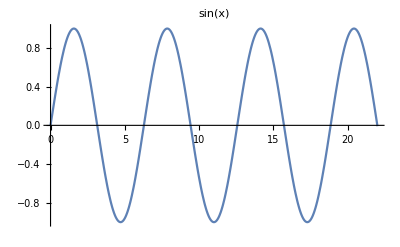

```mathematica
Plot[Sin[x],{x,0,22},PlotLabel->Style["sin(x)",FontSize->18]]
```